```mathematica
{#,5#^(2/5),10 #^(2/5)}&/@Range[10,500,50]//N//Round
{#[[1]],X->{-#[[2]],#[[2]],200},Y->{-#[[3]],#[[3]],200}}&/@%//ToString
StringDelete[StringReplace[%,"}, {"->"
"],{" ","{{","}}"}]
```

{{10,13,25},{60,26,51},{110,33,66},{160,38,76},{210,42,85},{260,46,92},{310,50,99},{360,53,105},{410,55,111},{460,58,116}}

{{10, X -> {-13, 13, 200}, Y -> {-25, 25, 200}}, {60, X -> {-26, 26, 200}, Y -> {-51, 51, 200}}, {110, X -> {-33, 33, 200}, Y -> {-66, 66, 200}}, {160, X -> {-38, 38, 200}, Y -> {-76, 76, 200}}, {210, X -> {-42, 42, 200}, Y -> {-85, 85, 200}}, {260, X -> {-46, 46, 200}, Y -> {-92, 92, 200}}, {310, X -> {-50, 50, 200}, Y -> {-99, 99, 200}}, {360, X -> {-53, 53, 200}, Y -> {-105, 105, 200}}, {410, X -> {-55, 55, 200}, Y -> {-111, 111, 200}}, {460, X -> {-58, 58, 200}, Y -> {-116, 116, 200}}}

10,X->{-13,13,200},Y->{-25,25,200}
60,X->{-26,26,200},Y->{-51,51,200}
110,X->{-33,33,200},Y->{-66,66,200}
160,X->{-38,38,200},Y->{-76,76,200}
210,X->{-42,42,200},Y->{-85,85,200}
260,X->{-46,46,200},Y->{-92,92,200}
310,X->{-50,50,200},Y->{-99,99,200}
360,X->{-53,53,200},Y->{-105,105,200}
410,X->{-55,55,200},Y->{-111,111,200}
460,X->{-58,58,200},Y->{-116,116,200}

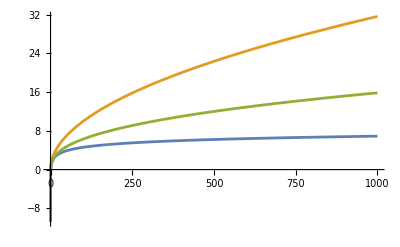

```mathematica
Plot[{Log[x],x^(1/2),x^(2/5)},{x,0,1000}]
```